# Assignment 10

Karim Sobh
201700836

## Problem 1

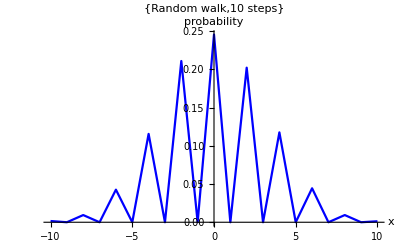

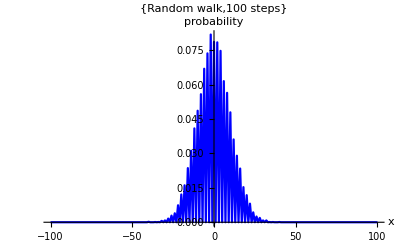

```mathematica
Clear["Global*`"]
nMax=10000;

For[time=10,time≤100,time *=10,
	x= Table[0, nMax];
	For[t=1, t≤time,t++,
			For[i=1,i≤nMax,i++,
			ran= RandomReal[];
			x[[i]] += Sign[ran-0.5];
		]
	];
	xRange= Range[-time,time,1];
	xcount = xRange 0;
	For[j=1, j≤Length[xRange],j++,
		xcount[[j]]= Count[x, xRange[[j]]];
	];
	xcount /= nMax;
	data=Transpose@{xRange,xcount};
	Print[ListLinePlot[data,AxesLabel->{"x", "probability"},PlotLabel->{"Random walk",time "steps"},PlotRange->All, PlotStyle->Blue]]
]
```

## Problem 10.2

Even Parity Energies

{0.497189,2.49292,4.49036,6.48829,8.48645}

odd Parity energies

{1.49998,3.49992,5.49981,7.49965,9.49943}

Exact Energies:

{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5}

ListPlot::nonopt: Options expected (instead of {{List,List},{0.,0.},{-0.01,0.00005},{-0.02,0.0002},{-0.03,0.00045},{-0.04,0.0008},{-0.05,0.00125},{-0.06,0.0018},{-0.07,0.00245},{-0.08,0.0032},{-0.09,0.00405},{-0.1,0.005},{-0.11,0.00605},{-0.12,0.0072},{-0.13,0.00845},{-0.14,0.0098},«20»,{-0.35,0.06125},{-0.36,0.0648},{-0.37,0.06845},{-0.38,0.0722},{-0.39,0.07605},{-0.4,0.08},{-0.41,0.08405},{-0.42,0.0882},{-0.43,0.09245},{-0.44,0.0968},{-0.45,0.10125},{-0.46,0.1058},{-0.47,0.11045},{-0.48,0.1152},«952»}) beyond position 1 in …. An option must be a rule or a list of rules.

Show::gtype: ListPlot is not a type of graphics.

Show[ListPlot[1],PlotRange→{{-5,5},{-5,5}}]
 |  |  |  |

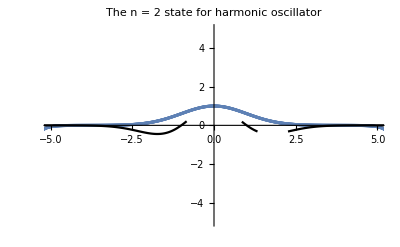

```mathematica
ClearAll["Global`*"]
xm = 10.0; dx = 0.01; 
x = Range[0, xm, dx]; lx = Length[x];
xs= Range[0, -xm, -dx]; lxs = Length[xs];
v = Table[0.0, {i,lx}];
Do[
v[[i]]=0.5*x[[i]]^2;
If[x[[i]]== 0.0,i0 = i]; 
,{i,lx}];
nEng = 5; 
engListEven = Table[0.0, {i,nEng}];
engListodd = Table[0.0, {i,nEng}];
plotEven1 = Table[0.0, {i,nEng}];plotEven2 = Table[0.0, {i,nEng}];
plotodd1 = Table[0.0, {i,nEng}];plotodd2 = Table[0.0, {i,nEng}];

eng = 0.1; 
psim = 2.0; 



(*Even solution*)
Do[
dE = .4; 


psi = Table[0.0, {i,lx}];
psi[[i0]] = 1.0; psi[[i0 -1]] = 1.0;  
i=i0+1;
While[Abs[psi[[i-1]]] < psim && i < lx,
psi[[i]] = 2.0 psi[[i-1]] - psi[[i-2]] - 2.0 (eng - v[[i-1]])psi[[i-1]] dx^2;  i++];
psiLast=psi[[i-1]] ; 

While[Abs[dE] > 0.000001,
psi = Table[0.0, {i,lx}];
psi[[i0]] = 1.0; psi[[i0 -1]] = 1.0;  
i=i0+1;
While[Abs[psi[[i-1]]] < psim && i < lx,
psi[[i]] = 2.0 psi[[i-1]] - psi[[i-2]] - 2.0 (eng - v[[i-1]])psi[[i-1]] dx^2;  i++];
psiNew=psi[[i-1]] ;
If[Sign[psiNew] != Sign[psiLast],eng = eng +dE ;dE=-dE/2.0;]; 
If[Sign[psiNew] == Sign[psiLast], eng = eng + dE];
psiLast =    psiNew];
engListEven[[j]] = eng;
eng = eng + 0.5;
ppsiEven1=Table[{x[[k]],psi[[k]]},{k,0,lx}];ppsiEven2=Table[{xs[[k]],psi[[k]]},{k,0,lx}];
plotEven1[[j]]=ListPlot[ppsiEven1,PlotRange->All];plotEven2[[j]]=ListPlot[ppsiEven2,PlotRange->All]
,{j,nEng}];

Clear[dE]
eng = 0.1; 
(*oddd solutions*)
Do[
dE = .4; 


psi = Table[0.0, {i,lx}];
psi[[i0]] = 0.0; psi[[i0 -1]] = -dx;  
i=i0+1;
While[Abs[psi[[i-1]]] < psim && i < lx,
psi[[i]] = 2.0 psi[[i-1]] - psi[[i-2]] - 2.0 (eng - v[[i-1]])psi[[i-1]] dx^2;  i++];
psiLast=psi[[i-1]] ; 

While[Abs[dE] > 0.00000001,
psi = Table[0.0, {i,lx}];
psi[[i0]] = 0.0; psi[[i0 -1]] = -dx;  
i=i0+1;
While[Abs[psi[[i-1]]] < psim && i < lx,
psi[[i]] = 2.0 psi[[i-1]] - psi[[i-2]] - 2.0 (eng - v[[i-1]])psi[[i-1]] dx^2;  i++];
psiNew=psi[[i-1]] ;
If[Sign[psiNew] != Sign[psiLast],eng = eng +dE ;dE=-dE/2.0;]; 
If[Sign[psiNew] == Sign[psiLast], eng = eng + dE];
psiLast =    psiNew];
engListodd[[j]] = eng;
eng = eng + 0.5;
ppsiodd1=Table[{x[[k]],psi[[k]]},{k,0,lx}];ppsiodd2=Table[{xs[[k]],psi[[k]]},{k,0,lx}];
plotodd1[[j]]=ListPlot[ppsiodd1,PlotRange->All];plotodd2[[j]]=ListPlot[ppsiodd2,PlotRange->All]
,{j,nEng}];



Print["Even Parity Energies"]
engListEven
Print["odd Parity energies"]
engListodd
Print["Exact Energies:"]
engExact =Table[n+0.5,{n,0,10,1}] 
vp=Table[{x[[i]],v[[i]]},{i,0,lx}];vp2=Table[{xs[[i]],v[[i]]},{i,0,lx}];
vpp=ListPlot[vp,vp2, Joined->True, AxesLabel->{"x","V(x)"},PlotStyle->Red];
Show[vpp,PlotRange-> {{-5,5},{-5,5}}]
ap1=Plot[(1-k^2) Exp[-k^2/2],{k,0,xm},PlotStyle->Black];ap2=Plot[(1-k^2) Exp[-k^2/2],{k,0,-xm},PlotStyle->Black];
Show[plotEven1[[1]],plotEven2[[1]],ap1,ap2,PlotRange-> {{-5,5},{-5,5}},PlotLabel->"The n = 1 state for harmonic oscillator"]
Show[plotEven1[[2]],plotEven2[[2]],ap1,ap2,PlotRange-> {{-5,5},{-5,5}},PlotLabel->"The n = 2 state for harmonic oscillator"]
Show[plotEven1[[3]],plotEven2[[3]],ap1,ap2,PlotRange-> {{-5,5},{-5,5}},PlotLabel->"The n = 3 state for harmonic oscillator"]
```

## Problem 10.1

Even Parity Energies:

{1.23989,11.1585,30.9933,60.7393,100.389}

odd Parity energies:

{4.98442,19.9364,44.8523,79.7259,124.548}

{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5}

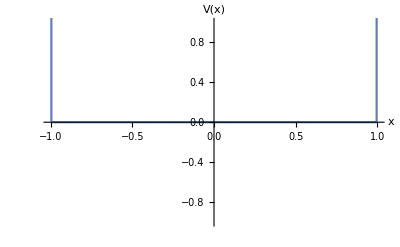

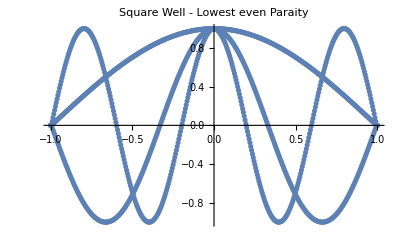

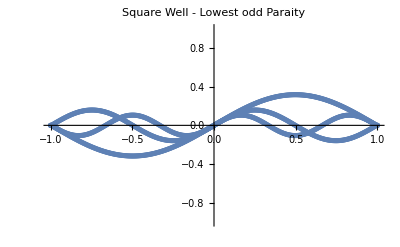

```mathematica
ClearAll["Global`*"]
xm = 1.0; dx = 0.005; 
x = Range[0, xm, dx]; lx = Length[x];
xs=Range[0,-xm,-dx];lxs=Length[xs];
v = Table[0.0, {i,lx}];
potEng=10000;
Do[
If[x[[i]]<= -1.0, v[[i]] = potEng];
If[x[[i]]>= 1.0, v[[i]] = potEng];
If[x[[i]]== 0.0,i0 = i]; l
,{i,lx}];
nEng = 5; 
engListEven = Table[0.0, {i,nEng}];
engListodd = Table[0.0, {i,nEng}];
plotEven1 =plotEven2= Table[0.0, {i,nEng}];
plotodd1=plotodd2 = Table[0.0, {i,nEng}];

eng = 0.1; 
psim = 2.0; 



(*Even solution*)
Do[
dE = .4; 


psi = Table[0.0, {i,lx}];
psi[[i0]] = 1.0; psi[[i0 -1]] = 1.0;  
i=i0+1;
While[Abs[psi[[i-1]]] < psim && i < lx,
psi[[i]] = 2.0 psi[[i-1]] - psi[[i-2]] - 2.0 (eng - v[[i-1]])psi[[i-1]] dx^2;  i++];
psiLast=psi[[i-1]] ; 

While[Abs[dE] > 0.000001,
psi = Table[0.0, {i,lx}];
psi[[i0]] = 1.0; psi[[i0 -1]] = 1.0;  
i=i0+1;
While[Abs[psi[[i-1]]] < psim && i < lx,
psi[[i]] = 2.0 psi[[i-1]] - psi[[i-2]] - 2.0 (eng - v[[i-1]])psi[[i-1]] dx^2;  i++];
psiNew=psi[[i-1]] ;
If[Sign[psiNew] != Sign[psiLast],eng = eng +dE ;dE=-dE/2.0;]; 
If[Sign[psiNew] == Sign[psiLast], eng = eng + dE];
psiLast =    psiNew];
engListEven[[j]] = eng;
eng = eng + 0.5;
ppsiEven1=Table[{x[[k]],psi[[k]]},{k,0,lx}];
ppaiEven2=Table[{xs[[k]],psi[[k]]},{k,0,lx}];
plotEven1[[j]]=ListPlot[ppsiEven1,PlotRange->All];plotEven2[[j]]=ListPlot[ppaiEven2,PlotRange->All],{j,nEng}];



Clear[dE]
eng = 0.1; 
(*odd solutions*)
Do[
dE = .4; 


psi = Table[0.0, {i,lx}];
psi[[i0]] = 0.0; psi[[i0 -1]] = -dx;  
i=i0+1;
While[Abs[psi[[i-1]]] < psim && i < lx,
psi[[i]] = 2.0 psi[[i-1]] - psi[[i-2]] - 2.0 (eng - v[[i-1]])psi[[i-1]] dx^2;  i++];
psiLast=psi[[i-1]] ; 

While[Abs[dE] > 0.00000001,
psi = Table[0.0, {i,lx}];
psi[[i0]] = 0.0; psi[[i0 -1]] = -dx;  
i=i0+1;
While[Abs[psi[[i-1]]] < psim && i < lx,
psi[[i]] = 2.0 psi[[i-1]] - psi[[i-2]] - 2.0 (eng - v[[i-1]])psi[[i-1]] dx^2;  i++];
psiNew=psi[[i-1]] ;
If[Sign[psiNew] != Sign[psiLast],eng = eng +dE ;dE=-dE/2.0;]; 
If[Sign[psiNew] == Sign[psiLast], eng = eng + dE];
psiLast =    psiNew];
engListodd[[j]] = eng;
eng = eng + 0.5;
ppsiodd1=Table[{x[[k]],psi[[k]]},{k,0,lx}];
ppsiodd2=Table[{xs[[k]],-psi[[k]]},{k,0,lx}];
plotodd1[[j]]=ListPlot[ppsiodd1,PlotRange->All]; plotodd2[[j]]=ListPlot[ppsiodd2,PlotRange->All]
,{j,nEng}];



Print["Even Parity Energies:"]
engListEven
Print["odd Parity energies:"]
engListodd

engExact =Table[n+0.5,{n,0,10,1}] 
vp1=Table[{x[[i]],v[[i]]},{i,0,lx}];
vp2=Table[{xs[[i]],v[[i]]},{i,0,lx}];
v2=ListPlot[vp2, Joined->True, AxesLabel->{"x","V(x)"}];
v1=ListPlot[vp1, Joined->True, AxesLabel->{"x","V(x)"}];
Show[v1,v2,PlotRange->{{-1,1},{-1,1}}]
Show[plotEven1[[1]],plotEven1[[2]],plotEven1[[3]],plotEven2[[1]],plotEven2[[2]],plotEven2[[3]],PlotRange-> {{-1,1},{-1,1}},PlotLabel->"Square Well - Lowest even Paraity"]
Show[plotodd1[[1]],plotodd2[[1]],plotodd1[[2]],plotodd2[[2]],plotodd1[[3]],plotodd2[[3]],PlotRange-> {{-1,1},{-1,1}},PlotLabel->"Square Well - Lowest odd Paraity"]
```

```mathematica
Problem 10.7
```

```mathematica
ClearAll["Global`*"]
xm = 20.0; dx = 0.05; 
x = Range[10^-10, xm, dx]; 
lx = Length[x];
v = Table[-1/x[[i]], {i,1,lx}];
i0=1; 
nEng = 2; 
color={Red,Green,Blue};
engList = Table[0.0, {i,nEng}];
plot = Table[0.0, {i,nEng}];
proplot=plot;
eng = -0.1; 
psim = 2.0; 
Do[
dE = -0.01; 


psi = Table[0.0, {i,lx}];
psi[[i0]] =0.0; psi[[i0 +1]] =0;  
i=i0+2;
While[Abs[psi[[i-1]]] < psim && i < lx,
psi[[i]] = 2.0 psi[[i-1]] - psi[[i-2]] +2( v[[i-1]]-eng )psi[[i-1]] dx^2;  i++];
psiLast=psi[[i-1]] ; 


While[Abs[dE] > 0.000000000001,
psi = Table[0.0, {i,lx}];
psi[[i0]] = 0.0; psi[[i0 +1]] =0.000001;  
i=i0+2;
While[Abs[psi[[i-1]]] < psim && i < lx,
psi[[i]] = (2.0 psi[[i-1]] - psi[[i-2]] +2( v[[i-1]]-eng )psi[[i-1]] dx^2);  i++];
psiNew=psi[[i-1]] ;
If[Sign[psiNew] == Sign[psiLast], eng = eng - dE]; 
If[Sign[psiNew] != Sign[psiLast],dE=-dE/2.0; eng = eng - dE];
psiLast = psiNew];
engList[[-j]] = eng;
eng = eng - 0.001;
psix=Table[{x[[t]],psi[[t]]*1/5*10^6},{t,1,lx}];
plot[[j]]=ListPlot[psix ,PlotRange->All,PlotStyle->If[j==1,Black,Red]];
psix2=Table[{x[[t]],psi[[t]]^2*10^9.1},{t,1,lx}];
proplot[[j]]=ListPlot[psix2,PlotRange->All,PlotStyle->If[j==1,Black,Red]]

,{j,nEng}];


Print["Calculated Eigenvalues"]
engList 
Print["Exact Eignevalues"]
engExact =Table[-1.0/(2 n^2),{n,2}] 
vx=Table[{x[[t]],v[[t]]},{t,1,lx}];
vp=ListPlot[vx, Joined->True, AxesLabel->{"x","V(x)"}];
Show[vp,plot[[1]],plot[[2]],PlotRange-> All,PlotLabel->"g for n=1 &2 "]

exp1=Plot[Exp[-2r],{r,10^-10,xm},PlotRange->All];
exp2=Plot[(1-r)^2 Exp[-r],{r,0,xm},PlotRange->All];
Show[proplot[[1]],exp2,PlotRange-> All,PlotLabel->"P(n=1) "]
Show[proplot[[2]],exp1,PlotRange-> All,PlotLabel->"P(n=2) "]
```

$Aborted

Calculated Eigenvalues

{-0.499688,-0.124967}

Exact Eignevalues

{-0.5,-0.125}

Part::partd: Part specification plot1⟦1⟧ is longer than depth of object.

Show::gcomb: Could not combine the graphics objects in Show[,,plot1⟦1⟧,PlotRange→All,PlotLabel→Ψ for n=1 &2 ].

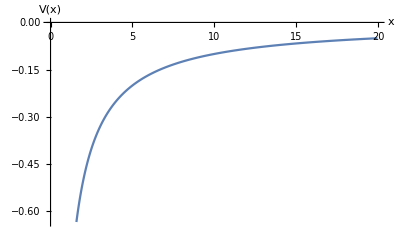
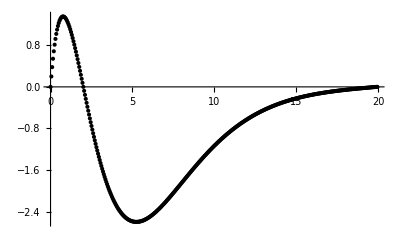
Show[-Graphics-,-Graphics-,plot1⟦1⟧,PlotRange→All,PlotLabel→Ψ for n=1 &2 ]

Show::gcomb: Could not combine the graphics objects in Show[Null ,,PlotRange→All,PlotLabel→P(l=1) ].

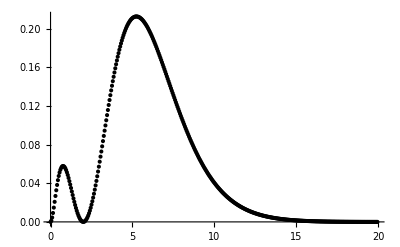
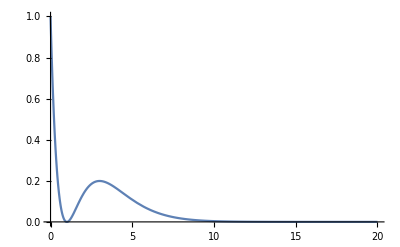
Show[Null -Graphics-,-Graphics-,PlotRange→All,PlotLabel→P(l=1) ]

Show::gcomb: Could not combine the graphics objects in Show[Null ,,PlotRange→All,PlotLabel→P(l=0) ].

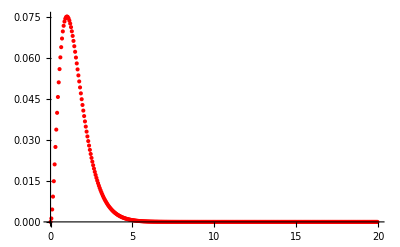
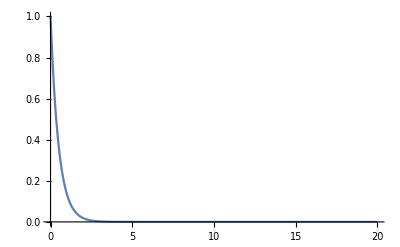
Show[Null -Graphics-,-Graphics-,PlotRange→All,PlotLabel→P(l=0) ]

```mathematica
ClearAll["Global`*"]
xm=20.0;dx=0.05;
x=Range[10^-10,xm,dx];
lx=Length[x];
v=Table[-1/x[[i]],{i,1,lx}];
ll2=Table[2/x[[i]]^2,{i,1,lx}];
i0=1;
nEng=2;
color={Red,Green,Blue};
engList=Table[0.0,{i,nEng}];
plot=Table[0.0,{i,nEng}];
proplot=plot;
eng=-0.1;
psim=2.0;
Do[dE=-0.01;
psi=Table[0.0,{i,lx}];
psi[[i0]]=0.0;psi[[i0+1]]=0;
i=i0+2;
While[Abs[psi[[i-1]]]<psim&&i<lx,psi[[i]]=2.0 psi[[i-1]]-psi[[i-2]]+ll2  psi[[i-1]] dx^2 +2 (v[[i-1]]-eng) psi[[i-1]] dx^2;i++];
psiLast=psi[[i-1]];
While[Abs[dE]>0.000000000001,psi=Table[0.0,{i,lx}];
psi[[i0]]=0.0;psi[[i0+1]]=0.000001;
i=i0+2;
While[Abs[psi[[i-1]]]<psim&&i<lx,psi[[i]]=(2.0 psi[[i-1]]-psi[[i-2]]+ll2  psi[[i-1]] dx^2+2 (v[[i-1]]-eng) psi[[i-1]] dx^2);i++];
psiNew=psi[[i-1]];
If[Sign[psiNew]==Sign[psiLast],eng=eng-dE];
If[Sign[psiNew]≠Sign[psiLast],dE=-dE/2.0;eng=eng-dE];
psiLast=psiNew];
engList[[-j]]=eng;
eng=eng-0.001;
psix=Table[{x[[t]],psi[[t]]*1/5*10^6},{t,1,lx}];
plot[[j]]=ListPlot[psix,PlotRange->All,PlotStyle->If[j==1,Black,Red]];
psix2=Table[{x[[t]],psi[[t]]^2*10^9.1},{t,1,lx}];
proplot[[j]]=ListPlot[psix2,PlotRange->All,PlotStyle->If[j==1,Black,Red]],{j,nEng}];


Print["Calculated Eigenvalues"]
engList
Print["Exact Eignevalues"]
engExact=Table[-1.0/(2 n^2),{n,2}]
vx=Table[{x[[t]],v[[t]]},{t,1,lx}];
vp=ListPlot[vx,Joined->True,AxesLabel->{"x","V(x)"}];
Show[vp,plot[[1]],plot[[2]],PlotRange->All,PlotLabel->"Ψ for n=1 &2 "]

exp1=Plot[Exp[-2 r],{r,10^-10,xm},PlotRange->All];
exp2=Plot[(1-r)^2 Exp[-r],{r,0,xm},PlotRange->All];
Show[proplot[[1]],exp2,PlotRange->All,PlotLabel->"P(n=1) "]
Show[proplot[[2]],exp1,PlotRange->All,PlotLabel->"P(n=2) "]
```